```mathematica
Exit[]
```

# QNMs of Halo Black Holes

```mathematica
(*Quit*)
```

```mathematica
(* non grid-based interpolation scheme to calculate QNMs of Schwarzschild black holes, I may have modified their method a bit. 
A HUGE CAUTION: any number you use has to be Rationalized or for large amount of grid points the code fail to work due to the differentiation matrices obtaining zero values*)
(* Main method taken from [arxiv:1610.08135v4] *)
```

```mathematica
SetDirectory[NotebookDirectory[]];
path=SetDirectory[NotebookDirectory[]];
```

```mathematica
<<HaloFlux`
```

```mathematica
n=15;
```

#### Differentiation matrices from built-in finite difference Mathematica functions

```mathematica
(*The above commented out code also calculates the differentiation matrices in the range we want but takes more time. It might be more accurate later when we deal with dirty black holes but for Schwarzschild the following method is enough.*)
min=0;
max=1;
 (*number of grid points used to discretize the metric components of spacetime, the compactified radial coordinate [0,1] and build the differentiation matrices*)
di=(max-min)/(n-1);(*equispaced data points*)
x=Table[i,{i,min,max,di}];
DF0=NDSolve`FiniteDifferenceDerivative[Derivative[0],Range[0,1,1/(n-1)],DifferenceOrder->n]["DifferentiationMatrix"] ;(*zeroth derivative*)
DF1=NDSolve`FiniteDifferenceDerivative[Derivative[1],Range[0,1,1/(n-1)],DifferenceOrder->n-1]["DifferentiationMatrix"]; (*first derivative*)
DF2=NDSolve`FiniteDifferenceDerivative[Derivative[2],Range[0,1,1/(n-1)],DifferenceOrder->n-2]["DifferentiationMatrix"]; (*second derivative*)
```

```mathematica
(* I delete the first and last entry in order to avoid calculating the functions at the extrema of the domain: 0 (rh) and 1 (∞), which are singular points *)
Delete[DF0,{{1},{n}}];
df0=Delete[Transpose[%],{{1},{n}}]//Transpose;
Delete[DF1,{{1},{n}}];
df1=Delete[Transpose[%],{{1},{n}}]//Transpose;
Delete[DF2,{{1},{n}}];
df2=Delete[Transpose[%],{{1},{n}}]//Transpose;
```

## Finding modes

#### function

```mathematica
δω[z_,l_,a0_,ωtrial_]:=Block[{mbh=1,M,ρmetric,f,m,fh,derfh,derrmh,rh,rc,r,t0,ω,l0,s0,Mt0,Ml0,Ms0,FM0,eq,sol},

rh=2mbh(1+10^-4);
M=a0 z;
rc=5*a0;(*rc=10*a0 for l=10*)

ρmetric=background["NFW",M,{a0,rc},10^13][[1,{1,3}]];(*ρmetric=background["NFW",M,{a0,rc},10^5][[1,{1,3}]] for l=10*)

f[r_]=ρmetric[[1,2]][r];(*(1-2/r)(1+(2 M)/(a0+2));*)
m[r_]=ρmetric[[2,2]][r];

fh=0;
derfh=(*(1-2z)/rh;*)f'[rh];
derrmh=(D[ρprofile[r,M,{a0,rc},"NFW"],r]//.r->rh)*16 π;

t0=Table[f[-rh/(-1+x⟦i⟧)] (2 m[-rh/(-1+x⟦i⟧)]+rh/(-1+x⟦i⟧)) (1-x⟦i⟧)^3 (-1+x⟦i⟧)^2 x⟦i⟧,{i,2,n-1}]//FullSimplify;

l0=Table[1/(√(rh derfh))f[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧)^2 (2 m[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧) ((-1+x⟦i⟧) (-2+(1+4 ⅈ M ω) x⟦i⟧) √(rh derfh)+2 ⅈ rh ω (1-2 x⟦i⟧ (1+√(rh derfh))+x⟦i⟧^2 (1+√(rh derfh))))+rh (2 (-1+x⟦i⟧) (-1+(1+2 ⅈ M ω) x⟦i⟧) √(rh derfh)+2 ⅈ rh ω (1-2 x⟦i⟧ (1+√(rh derfh))+x⟦i⟧^2 (1+√(rh derfh)))-(-1+x⟦i⟧) x⟦i⟧ √(rh derfh)(m'[-rh/(-1+x⟦i⟧)]))),{i,2,n-1}]//FullSimplify;

s0=Table[1/(x⟦i⟧ derfh)f[-rh/(-1+x⟦i⟧)] (rh+2 m[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧)) ((-2+2 (5+2 ⅈ M ω+2 ⅈ rh ω) x⟦i⟧+(-20-17 ⅈ rh ω+4 M^2 ω^2+4 rh^2 ω^2+2 M ω (-9 ⅈ+4 rh ω)) x⟦i⟧^2-2 (-9-9 ⅈ rh ω+4 M^2 ω^2+2 rh^2 ω^2+6 M ω (-2 ⅈ+rh ω)) x⟦i⟧^3+(-6-5 ⅈ rh ω+4 M^2 ω^2+rh^2 ω^2+2 M ω (-5 ⅈ+2 rh ω)) x⟦i⟧^4) derfh+ω (-1+x⟦i⟧)^2 ((-1+x⟦i⟧) (3 ⅈ+(-5 ⅈ+4 M ω) x⟦i⟧) √(rh derfh)+rh ω (1-2 x⟦i⟧ (1+2 √(rh derfh))+x⟦i⟧^2 (1+2 √(rh derfh)))))+1/(√(rh derfh))f[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧) ((-1+x⟦i⟧) (-1+(2+2 ⅈ M ω) x⟦i⟧) √(rh derfh)+ⅈ rh ω (1-2 x⟦i⟧ (1+√(rh derfh))+x⟦i⟧^2 (1+√(rh derfh)))) (6 m[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧)+rh (2+m'[-rh/(-1+x⟦i⟧)]))+(1-x⟦i⟧)^3 x⟦i⟧ ((rh^3 ω^2)/(-1+x⟦i⟧)^3+f[-rh/(-1+x⟦i⟧)] (-6 m[-rh/(-1+x⟦i⟧)]-(rh (l+l^2+m'[-rh/(-1+x⟦i⟧)]))/(-1+x⟦i⟧))),{i,2,n-1}]//FullSimplify;

Mt0=t0*IdentityMatrix[n-2];
Ml0=l0*IdentityMatrix[n-2];
Ms0=s0*IdentityMatrix[n-2];

(*ωtrial=SetPrecision[0.37-0.08I,50];*)

FM0=Mt0.df2+Ml0.df1+Ms0.df0;
eq=Det[N[FM0,Precision[FM0]]];

sol=FindRoot[eq==0,{ω,ωtrial},WorkingPrecision->Precision[eq]];
PrintTemporary[{Re[sol[[1,2]]],Im[sol[[1,2]]]}];
Return[{z,Re[sol[[1,2]]],Im[sol[[1,2]]]}]
]
```

```mathematica
compactness=List[10^-6,10^-2,2 10^-2,4 10^-2,6 10^-2,8 10^-2, 10^-1];
compactness10=List[10^-6,10^-3,2 10^-3,4 10^-3,6 10^-3,8 10^-3, 10^-2];
```

#### fundamental

```mathematica
Nl2n0=Monitor[Table[δω[compactness[[ii]],2,17,SetPrecision[0.374-0.089I,50]],{ii,1,Length[compactness]}],ii];
ReImNl2n0=Nl2n0[[;;,2;;3]];
```

```mathematica
Nl3n0=Monitor[Table[δω[compactness[[ii]],3,17,SetPrecision[0.599-0.092I,50]],{ii,1,Length[compactness]}],ii];
ReImNl3n0=Nl3n0[[;;,2;;3]];
```

```mathematica
Nl4n0=Monitor[Table[δω[compactness[[ii]],4,16,SetPrecision[0.809-0.094I,50]],{ii,1,Length[compactness]}],ii];
ReImNl4n0=Nl4n0[[;;,2;;3]];
```

```mathematica
Nl10n0=Monitor[Table[δω[compactness[[ii]],10,12,SetPrecision[1.99678579733-0.0958637762I,50]],{ii,1,Length[compactness]}],ii];
ReImNl10n0=Nl10n0[[;;,2;;3]];
```

#### first overtone

```mathematica
Nl2n1=Monitor[Table[δω[compactness[[ii]],2,5,SetPrecision[0.346-0.274I,50]],{ii,1,Length[compactness]}],ii];
ReImNl2n1=Nl2n1[[;;,2;;3]];
```

```mathematica
Nl3n1=Monitor[Table[δω[compactness[[ii]],3,9,SetPrecision[0.58-0.28I,50]],{ii,1,Length[compactness]}],ii];
ReImNl3n1=Nl3n1[[;;,2;;3]];
```

```mathematica
Nl4n1=Monitor[Table[δω[compactness[[ii]],4,9,SetPrecision[0.79-0.28I,50]],{ii,1,Length[compactness]}],ii];
ReImNl4n1=Nl4n1[[;;,2;;3]];
```

```mathematica
Nl10n1=Monitor[Table[δω[compactness[[ii]],10,6,SetPrecision[1.991-0.287I,50]],{ii,1,Length[compactness]}],ii];
ReImNl10n1=Nl10n1[[;;,2;;3]]
```

#### second overtone

```mathematica
Nl2n2=Monitor[Table[δω[compactness[[ii]],2,5,SetPrecision[0.30105-0.47827I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
Nl3n2=Monitor[Table[δω[compactness[[ii]],3,5,SetPrecision[0.56-0.48I,50]],{ii,1,Length[compactness]}],ii];
```

Divide::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

FindRoot::jsing: Encountered a singular Jacobian at the point {ω} = {0.47038856946464225113380375496911813275980877741501-0.58976673741476837972719492512261841503279384531816 ⅈ}. Try perturbing the initial point(s).

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 51.0625 digits of working precision to meet these tolerances.

```mathematica
Nl4n2=Monitor[Table[δω[compactness[[ii]],4,5,SetPrecision[0.80-0.48I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
ReImNl2n2=Nl2n2[[;;,2;;3]];
ReImNl3n2=Nl3n2[[;;,2;;3]];
ReImNl4n2=Nl4n2[[;;,2;;3]];
```

## Export

```mathematica
Export["Matrix_NFW_ln.m",{ReImNl2n0,ReImNl3n0,ReImNl4n0,ReImNl10n0,ReImNl2n1,ReImNl3n1,ReImNl4n1,ReImNl10n1}]
```

Matrix_NFW_ln.m

## Plot

```mathematica
xlnu=Join[Table[{i,,{0.0005,0}},{i,-0.31,0.01,0.01}],Table[{1i,,{0.01,0}},{i,-0.3,0.007,0.05}]];
```

```mathematica
{ReImNl2n0,ReImNl3n0,ReImNl4n0,ReImNl10n0,ReImNl2n1,ReImNl3n1,ReImNl4n1,ReImNl10n1}=Import["Matrix_NFW_ln.m"];
```

#### all

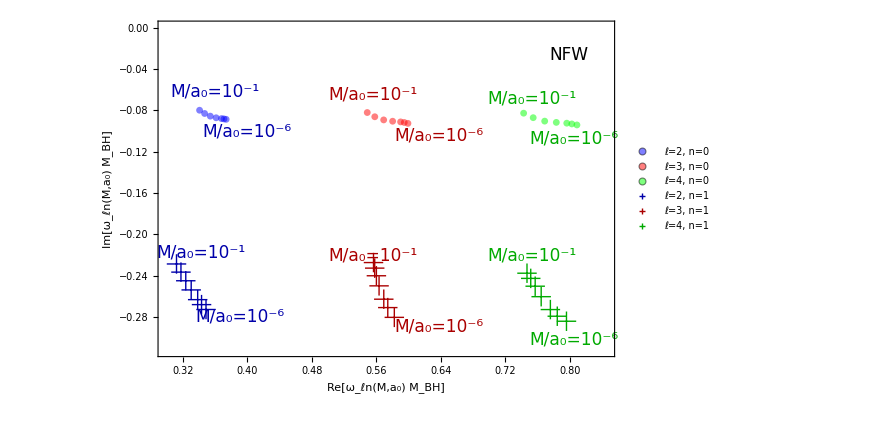

./plot/NFW_234_01.pdf

```mathematica
ln01=ListPlot[{ReImNl2n0,ReImNl3n0,ReImNl4n0,ReImNl2n1,ReImNl3n1,ReImNl4n1},Frame->True,ImageSize->650,PlotRange->{{0.3,0.845},{-0.312,-0.0}},FrameStyle->Directive[Thickness[0.0025],Black],FrameTicks->True,FrameLabel->{Style["Re[ω_ℓn(M,a_0) M_BH]",Black,20],Style["Im[ω_ℓn(M,a_0) M_BH]",Black,20]},FrameTicksStyle->Directive[Black,20],LabelStyle->{FontSize->19,FontFamily->"Times"},PlotMarkers->{Graphics[{Blue,Opacity[0.5],Thick,Disk[]},ImageSize->7],Graphics[{Red,Opacity[0.5],Thick,Disk[]},ImageSize->7],Graphics[{Green,Opacity[0.5],Thick,Disk[]},ImageSize->7],Style["+",{Darker@Blue,FontSize->20}],Style["+",{Darker@Red,FontSize->20}],Style["+",{Darker@Green,FontSize->20}]},PlotLegends->Placed[LineLegend[{Style["ℓ=2, n=0",FontSize->16],Style["ℓ=3, n=0",FontSize->16],Style["ℓ=4, n=0",FontSize->16],Style["ℓ=2, n=1",FontSize->16],Style["ℓ=3, n=1",FontSize->16],Style["ℓ=4, n=1",FontSize->16]},LegendLayout->{"Column",2},"Spacings"->{0.3}],{0.2,0.47}],ImagePadding->{{90, 50}, {70,10}},AspectRatio->0.65,Epilog->{Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Blue],Scaled[{0.195,0.67}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Blue],Scaled[{0.125,0.79}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Red],Scaled[{0.615,0.66}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Red],Scaled[{0.47,0.78}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Green],Scaled[{0.91,0.65}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Green],Scaled[{0.82,0.77}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Blue],Scaled[{0.18,0.12}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Blue],Scaled[{0.095,0.31}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Red],Scaled[{0.615,0.09}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Red],Scaled[{0.47,0.30}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Green],Scaled[{0.91,0.05}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Green],Scaled[{0.82,0.30}]],
Text[Style["NFW",17,FontFamily->"Palatino",Black],Scaled[{0.9,0.9}]]}]
Export["./plot/NFW_234_01.pdf",%]
```

#### all l

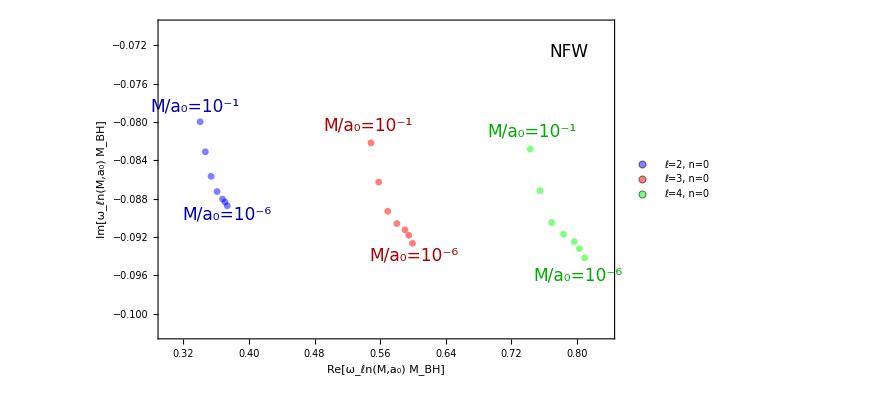

./plot/NFW_234_0.pdf

```mathematica
ln0=ListPlot[{ReImNl2n0,ReImNl3n0,ReImNl4n0},Frame->True,ImageSize->650,PlotRange->{{0.3,0.835},{-0.102,-0.07}},FrameStyle->Directive[Thickness[0.0025],Black],FrameTicks->True,FrameLabel->{Style["Re[ω_ℓn(M,a_0) M_BH]",Black,20],Style["Im[ω_ℓn(M,a_0) M_BH]",Black,20]},FrameTicksStyle->Directive[Black,20],LabelStyle->{FontSize->19,FontFamily->"Times"},PlotMarkers->{Graphics[{Blue,Opacity[0.5],Thick,Disk[]},ImageSize->7],Graphics[{Red,Opacity[0.5],Thick,Disk[]},ImageSize->7],Graphics[{Green,Opacity[0.5],Thick,Disk[]},ImageSize->7],Style["+",{Darker@Blue,FontSize->20}],Style["+",{Darker@Red,FontSize->20}],Style["+",{Darker@Green,FontSize->20}]},PlotLegends->Placed[LineLegend[{Style["ℓ=2, n=0",FontSize->16],Style["ℓ=3, n=0",FontSize->16],Style["ℓ=4, n=0",FontSize->16],Style["ℓ=2, n=1",FontSize->16],Style["ℓ=3, n=1",FontSize->16],Style["ℓ=4, n=1",FontSize->16]},"Spacings"->{0.3}],{0.1,0.2}],Epilog->{Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Blue],Scaled[{0.15,0.39}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Blue],Scaled[{0.08,0.73}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Red],Scaled[{0.56,0.26}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Red],Scaled[{0.46,0.67}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Green],Scaled[{0.92,0.2}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Green],Scaled[{0.82,0.65}]],
Text[Style["NFW",17,FontFamily->"Palatino",Black],Scaled[{0.9,0.9}]]}]
Export["./plot/NFW_234_0.pdf",%]
```

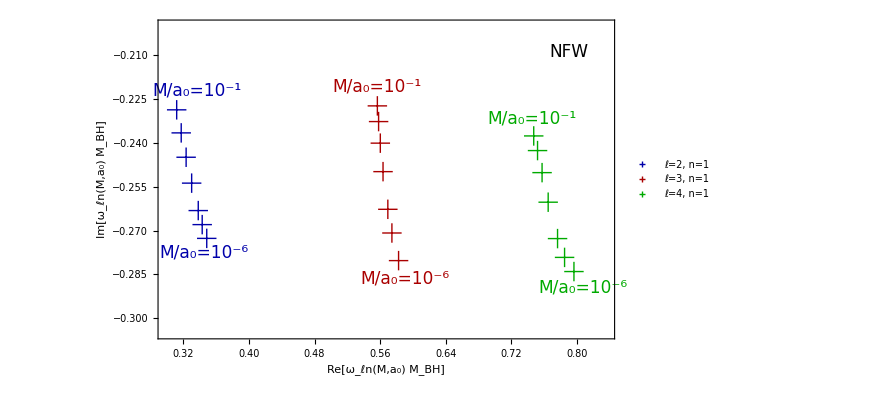

./plot/NFW_234_1.pdf

```mathematica
ln1=ListPlot[{ReImNl2n1,ReImNl3n1,ReImNl4n1},Frame->True,ImageSize->650,PlotRange->{{0.3,0.835},{-0.305,-0.20}},FrameStyle->Directive[Thickness[0.0025],Black],FrameTicks->True,FrameLabel->{Style["Re[ω_ℓn(M,a_0) M_BH]",Black,20],Style["Im[ω_ℓn(M,a_0) M_BH]",Black,20]},FrameTicksStyle->Directive[Black,20],LabelStyle->{FontSize->19,FontFamily->"Times"},PlotMarkers->{Style["+",{Darker@Blue,FontSize->20}],Style["+",{Darker@Red,FontSize->20}],Style["+",{Darker@Green,FontSize->20}]},PlotLegends->Placed[LineLegend[{Style["ℓ=2, n=1",FontSize->16],Style["ℓ=3, n=1",FontSize->16],Style["ℓ=4, n=1",FontSize->16]},"Spacings"->{0.3}],{0.1,0.12}],Epilog->{Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Blue],Scaled[{0.10,0.27}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Blue],Scaled[{0.085,0.78}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Red],Scaled[{0.54,0.19}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Red],Scaled[{0.48,0.79}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Green],Scaled[{0.93,0.16}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Green],Scaled[{0.82,0.69}]],
Text[Style["NFW",17,FontFamily->"Palatino",Black],Scaled[{0.9,0.9}]]}]
Export["./plot/NFW_234_1.pdf",%]
```

#### all n

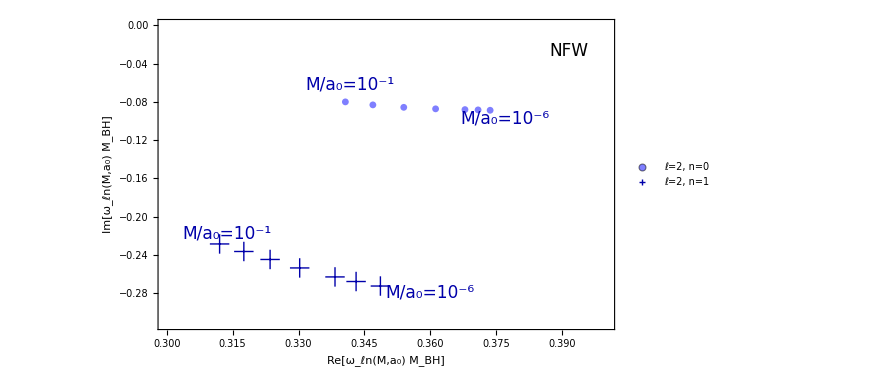

./plot/NFW_01_2.pdf

```mathematica
l2n=ListPlot[{ReImNl2n0,ReImNl2n1},Frame->True,ImageSize->650,PlotRange->{{0.3,0.4},{-0.312,-0.}},FrameStyle->Directive[Thickness[0.0025],Black],FrameTicks->True,FrameLabel->{Style["Re[ω_ℓn(M,a_0) M_BH]",Black,20],Style["Im[ω_ℓn(M,a_0) M_BH]",Black,20]},FrameTicksStyle->Directive[Black,20],LabelStyle->{FontSize->19,FontFamily->"Times"},PlotMarkers->{Graphics[{Blue,Opacity[0.5],Thick,Disk[]},ImageSize->7],Style["+",{Darker@Blue,FontSize->20}],Style["+",{Darker@Red,FontSize->20}],Style["+",{Darker@Green,FontSize->20}]},PlotLegends->Placed[LineLegend[{Style["ℓ=2, n=0",FontSize->16],Style["ℓ=2, n=1",FontSize->16],Style["ℓ=4, n=0",FontSize->16],Style["ℓ=2, n=1",FontSize->16],Style["ℓ=3, n=1",FontSize->16],Style["ℓ=4, n=1",FontSize->16]},"Spacings"->{0.3}],{0.85,0.15}],ImagePadding->{{90, 50}, {70,10}},AspectRatio->0.6,Epilog->{Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Blue],Scaled[{0.42,0.79}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Blue],Scaled[{0.76,0.68}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Blue],Scaled[{0.595,0.12}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Blue],Scaled[{0.15,0.31}]],
Text[Style["NFW",17,FontFamily->"Palatino",Black],Scaled[{0.9,0.9}]]}]
Export["./plot/NFW_01_2.pdf",%]
```

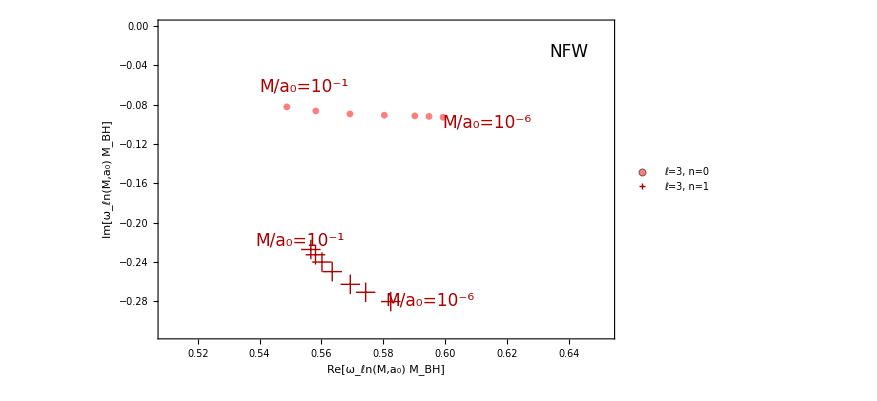

./plot/NFW_01_3.pdf

```mathematica
l3n=ListPlot[{ReImNl3n0,ReImNl3n1},Frame->True,ImageSize->650,PlotRange->{{0.51,0.652},{-0.312,-0.}},FrameStyle->Directive[Thickness[0.0025],Black],FrameTicks->True,FrameLabel->{Style["Re[ω_ℓn(M,a_0) M_BH]",Black,20],Style["Im[ω_ℓn(M,a_0) M_BH]",Black,20]},FrameTicksStyle->Directive[Black,20],LabelStyle->{FontSize->19,FontFamily->"Times"},PlotMarkers->{Graphics[{Red,Opacity[0.5],Thick,Disk[]},ImageSize->7],Style["+",{Darker@Red,FontSize->20}],Style["+",{Darker@Red,FontSize->20}],Style["+",{Darker@Green,FontSize->20}]},PlotLegends->Placed[LineLegend[{Style["ℓ=3, n=0",FontSize->16],Style["ℓ=3, n=1",FontSize->16],Style["ℓ=4, n=0",FontSize->16],Style["ℓ=2, n=1",FontSize->16],Style["ℓ=3, n=1",FontSize->16],Style["ℓ=4, n=1",FontSize->16]},"Spacings"->{0.3}],{0.85,0.15}],Epilog->{Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Red],Scaled[{0.32,0.79}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Red],Scaled[{0.72,0.68}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Red],Scaled[{0.595,0.12}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Red],Scaled[{0.31,0.31}]],
Text[Style["NFW",17,FontFamily->"Palatino",Black],Scaled[{0.9,0.9}]]}]
Export["./plot/NFW_01_3.pdf",%]
```

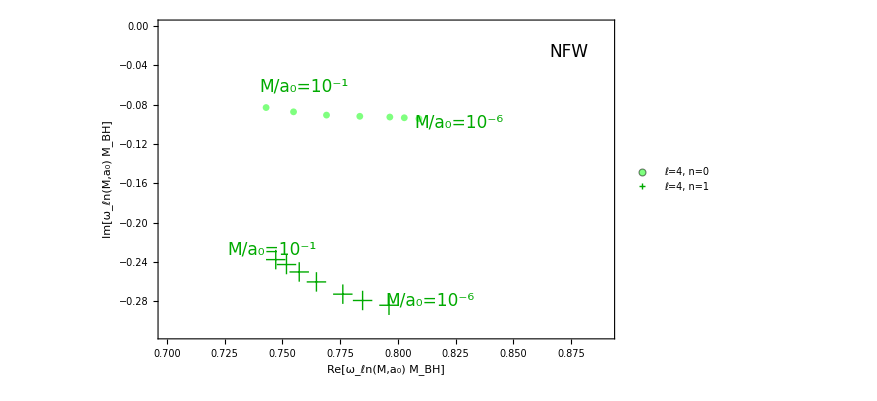

./plot/NFW_01_4.pdf

```mathematica
l4n=ListPlot[{ReImNl4n0,ReImNl4n1},Frame->True,ImageSize->650,PlotRange->{{0.7,0.89},{-0.312,-0.}},FrameStyle->Directive[Thickness[0.0025],Black],FrameTicks->True,FrameLabel->{Style["Re[ω_ℓn(M,a_0) M_BH]",Black,20],Style["Im[ω_ℓn(M,a_0) M_BH]",Black,20]},FrameTicksStyle->Directive[Black,20],LabelStyle->{FontSize->19,FontFamily->"Times"},PlotMarkers->{Graphics[{Green,Opacity[0.5],Thick,Disk[]},ImageSize->7],Style["+",{Darker@Green,FontSize->20}],Style["+",{Darker@Green,FontSize->20}],Style["+",{Darker@Green,FontSize->20}]},PlotLegends->Placed[LineLegend[{Style["ℓ=4, n=0",FontSize->16],Style["ℓ=4, n=1",FontSize->16],Style["ℓ=4, n=0",FontSize->16],Style["ℓ=2, n=1",FontSize->16],Style["ℓ=3, n=1",FontSize->16],Style["ℓ=4, n=1",FontSize->16]},"Spacings"->{0.3}],{0.85,0.15}],Epilog->{Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Green],Scaled[{0.32,0.79}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Green],Scaled[{0.66,0.68}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Green],Scaled[{0.595,0.12}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Green],Scaled[{0.25,0.28}]],
Text[Style["NFW",17,FontFamily->"Palatino",Black],Scaled[{0.9,0.9}]]}]
Export["./plot/NFW_01_4.pdf",%]
```

#### 10

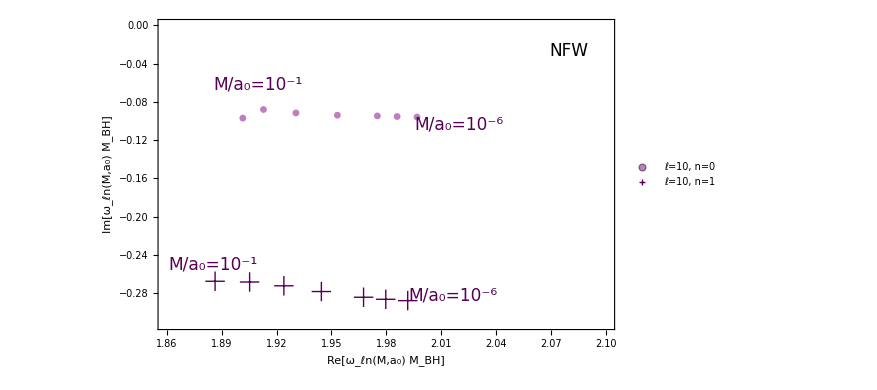

./plot/NFW_01_10.pdf

```mathematica
l10n=ListPlot[{ReImNl10n0,ReImNl10n1},Frame->True,ImageSize->650,PlotRange->{{1.86,2.1},{-0.312,-0.}},FrameStyle->Directive[Thickness[0.0025],Black],FrameTicks->True,FrameLabel->{Style["Re[ω_ℓn(M,a_0) M_BH]",Black,20],Style["Im[ω_ℓn(M,a_0) M_BH]",Black,20]},FrameTicksStyle->Directive[Black,20],LabelStyle->{FontSize->19,FontFamily->"Times"},PlotMarkers->{Graphics[{Purple,Opacity[0.5],Thick,Disk[]},ImageSize->7],Style["+",{Darker@Purple,FontSize->20}],Style["+",{Darker@Purple,FontSize->20}],Style["+",{Darker@Purple,FontSize->20}]},PlotLegends->Placed[LineLegend[{Style["ℓ=10, n=0",FontSize->16],Style["ℓ=10, n=1",FontSize->16],Style["ℓ=, n=0",FontSize->16],Style["ℓ=2, n=1",FontSize->16],Style["ℓ=3, n=1",FontSize->16],Style["ℓ=4, n=1",FontSize->16]},"Spacings"->{0.3}],{0.85,0.15}],ImagePadding->{{90, 50}, {70,10}},AspectRatio->0.6,Epilog->{Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Purple],Scaled[{0.22,0.79}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Purple],Scaled[{0.66,0.66}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Purple],Scaled[{0.645,0.11}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Purple],Scaled[{0.12,0.21}]],
Text[Style["NFW",17,FontFamily->"Palatino",Black],Scaled[{0.9,0.9}]]}]
Export["./plot/NFW_01_10.pdf",%]
```

#### more els and ens

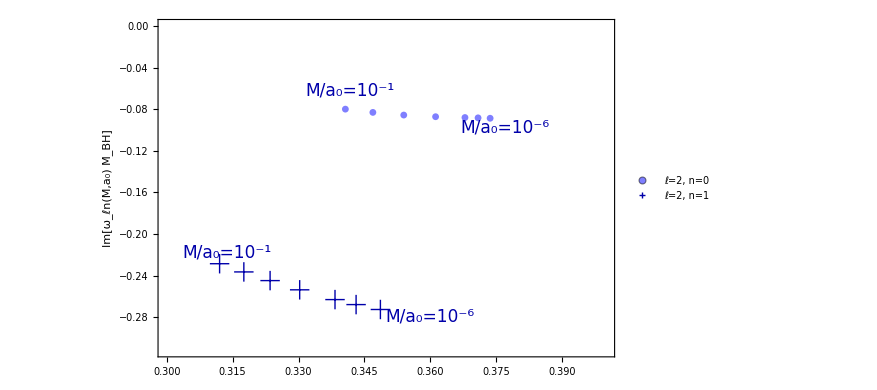

```mathematica
l2nA=ListPlot[{ReImNl2n0,ReImNl2n1},Frame->True,ImageSize->650,PlotRange->{{0.3,0.4},{-0.312,-0.}},FrameStyle->Directive[Thickness[0.0025],Black],FrameTicks->True,FrameLabel->{None,Style["Im[ω_ℓn(M,a_0) M_BH]",Black,20]},FrameTicksStyle->Directive[Black,20],LabelStyle->{FontSize->19,FontFamily->"Times"},PlotMarkers->{Graphics[{Blue,Opacity[0.5],Thick,Disk[]},ImageSize->7],Style["+",{Darker@Blue,FontSize->20}],Style["+",{Darker@Red,FontSize->20}],Style["+",{Darker@Green,FontSize->20}]},PlotLegends->Placed[LineLegend[{Style["ℓ=2, n=0",FontSize->16],Style["ℓ=2, n=1",FontSize->16],Style["ℓ=4, n=0",FontSize->16],Style["ℓ=2, n=1",FontSize->16],Style["ℓ=3, n=1",FontSize->16],Style["ℓ=4, n=1",FontSize->16]},"Spacings"->{0.3}],{0.85,0.15}],ImagePadding->{{90, 20}, {70,10}},AspectRatio->0.6,Epilog->{Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Blue],Scaled[{0.42,0.79}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Blue],Scaled[{0.76,0.68}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Blue],Scaled[{0.595,0.12}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Blue],Scaled[{0.15,0.31}]]}]
```

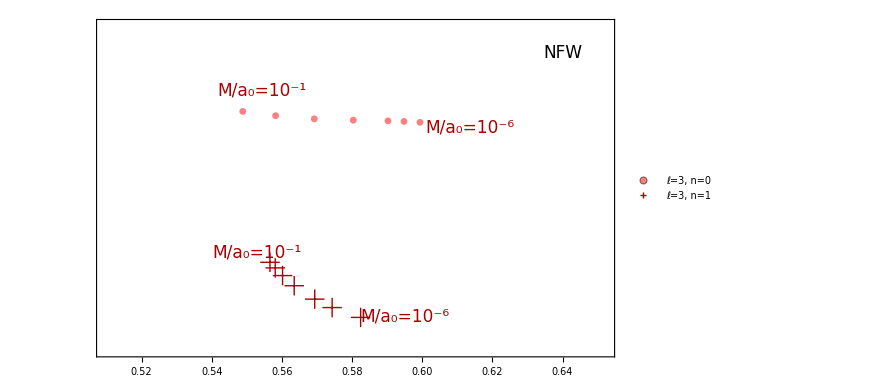

```mathematica
l3nA=ListPlot[{ReImNl3n0,ReImNl3n1},Frame->True,ImageSize->650,PlotRange->{{0.51,0.652},{-0.312,-0.}},FrameStyle->Directive[Thickness[0.0025],Black],FrameTicks->{{xlnu,xlnu},{Automatic,Automatic}},FrameLabel->{None,None},FrameTicksStyle->Directive[Black,20],LabelStyle->{FontSize->19,FontFamily->"Times"},PlotMarkers->{Graphics[{Red,Opacity[0.5],Thick,Disk[]},ImageSize->7],Style["+",{Darker@Red,FontSize->20}],Style["+",{Darker@Red,FontSize->20}],Style["+",{Darker@Green,FontSize->20}]},PlotLegends->Placed[LineLegend[{Style["ℓ=3, n=0",FontSize->16],Style["ℓ=3, n=1",FontSize->16]},"Spacings"->{0.3}],{0.85,0.15}],ImagePadding->{{90, 20}, {70,10}},AspectRatio->0.6,Epilog->{Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Red],Scaled[{0.32,0.79}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Red],Scaled[{0.72,0.68}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Red],Scaled[{0.595,0.12}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Red],Scaled[{0.31,0.31}]],
Text[Style["NFW",17,FontFamily->"Palatino",Black],Scaled[{0.9,0.9}]]}]
```

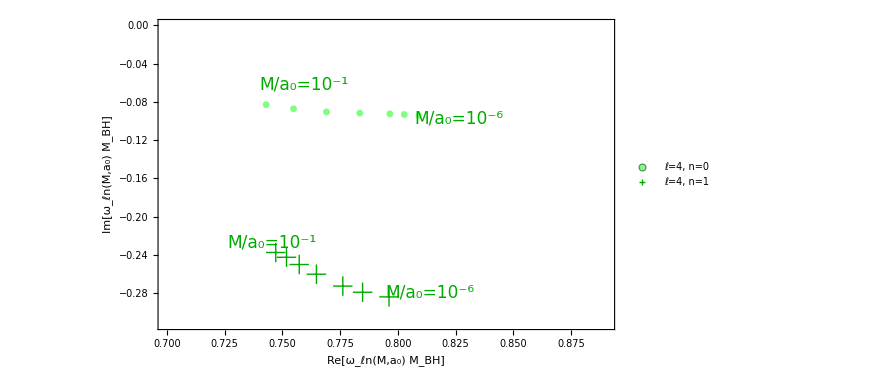

```mathematica
l4nA=ListPlot[{ReImNl4n0,ReImNl4n1},Frame->True,ImageSize->650,PlotRange->{{0.7,0.89},{-0.312,-0.}},FrameStyle->Directive[Thickness[0.0025],Black],FrameTicks->True,FrameLabel->{Style["Re[ω_ℓn(M,a_0) M_BH]",Black,20],Style["Im[ω_ℓn(M,a_0) M_BH]",Black,20]},FrameTicksStyle->Directive[Black,20],LabelStyle->{FontSize->19,FontFamily->"Times"},PlotMarkers->{Graphics[{Green,Opacity[0.5],Thick,Disk[]},ImageSize->7],Style["+",{Darker@Green,FontSize->20}],Style["+",{Darker@Green,FontSize->20}],Style["+",{Darker@Green,FontSize->20}]},PlotLegends->Placed[LineLegend[{Style["ℓ=4, n=0",FontSize->16],Style["ℓ=4, n=1",FontSize->16],Style["ℓ=4, n=0",FontSize->16],Style["ℓ=2, n=1",FontSize->16],Style["ℓ=3, n=1",FontSize->16],Style["ℓ=4, n=1",FontSize->16]},"Spacings"->{0.3}],{0.85,0.15}],ImagePadding->{{90, 20}, {70,10}},AspectRatio->0.6,Epilog->{Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Green],Scaled[{0.32,0.79}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Green],Scaled[{0.66,0.68}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Green],Scaled[{0.595,0.12}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Green],Scaled[{0.25,0.28}]]}]
```

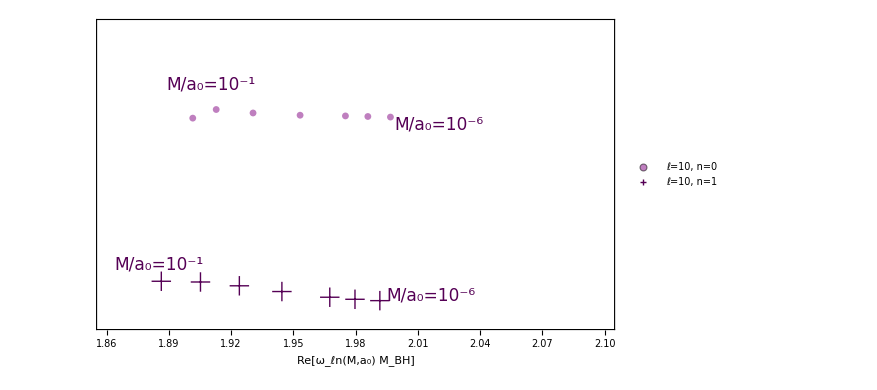

```mathematica
l10nA=ListPlot[{ReImNl10n0,ReImNl10n1},Frame->True,ImageSize->650,PlotRange->{{1.86,2.1},{-0.312,-0.}},FrameStyle->Directive[Thickness[0.0025],Black],FrameTicks->{{xlnu,xlnu},{Automatic,Automatic}},FrameLabel->{Style["Re[ω_ℓn(M,a_0) M_BH]",Black,20],None},FrameTicksStyle->Directive[Black,20],LabelStyle->{FontSize->19,FontFamily->"Times"},PlotMarkers->{Graphics[{Purple,Opacity[0.5],Thick,Disk[]},ImageSize->7],Style["+",{Darker@Purple,FontSize->20}],Style["+",{Darker@Purple,FontSize->20}],Style["+",{Darker@Purple,FontSize->20}]},PlotLegends->Placed[LineLegend[{Style["ℓ=10, n=0",FontSize->16],Style["ℓ=10, n=1",FontSize->16],Style["ℓ=, n=0",FontSize->16],Style["ℓ=2, n=1",FontSize->16],Style["ℓ=3, n=1",FontSize->16],Style["ℓ=4, n=1",FontSize->16]},"Spacings"->{0.3}],{0.85,0.15}],ImagePadding->{{90, 20}, {70,10}},AspectRatio->0.6,Epilog->{Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Purple],Scaled[{0.22,0.79}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Purple],Scaled[{0.66,0.66}]],Text[Style["M/a_0=10^-6",17,FontFamily->"Times",Darker@Purple],Scaled[{0.645,0.11}]],Text[Style["M/a_0=10^-1",17,FontFamily->"Times",Darker@Purple],Scaled[{0.12,0.21}]]}]
```

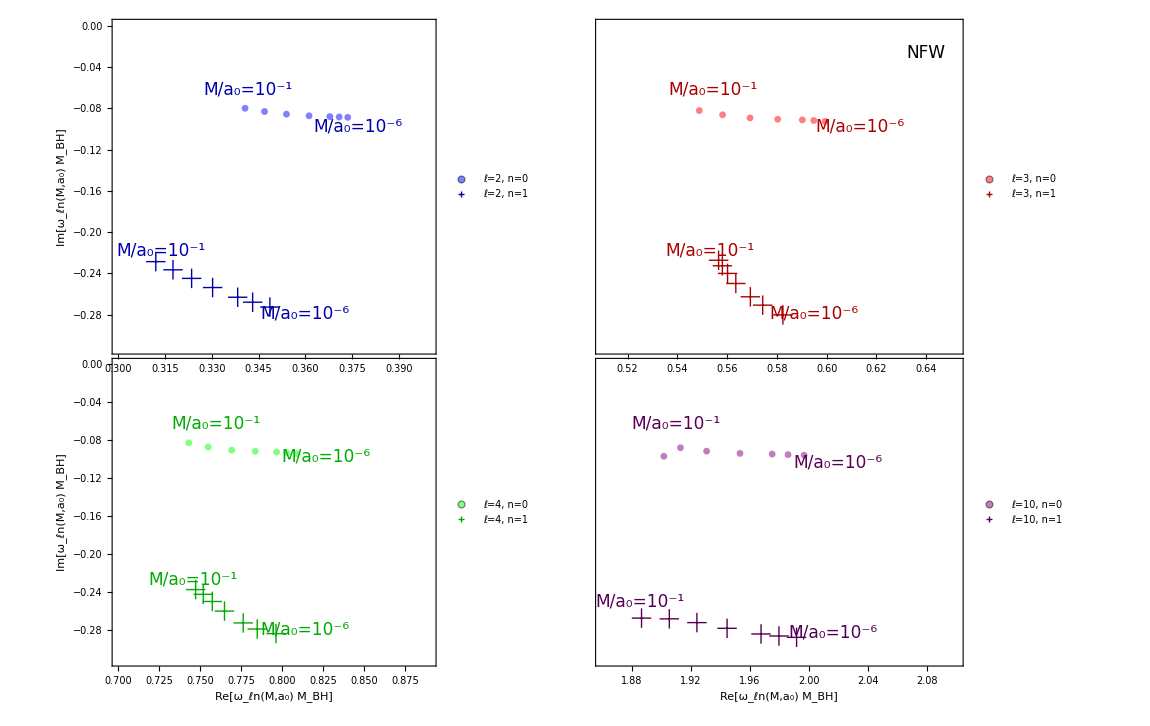

./plot/NFW_Grid_different_ln.pdf

```mathematica
GraphicsGrid[{{l2nA,l3nA},{l4nA,l10nA}},ImageSize->1150,Spacings->{{-20,-100},{-20,-50}}]
Export["./plot/NFW_Grid_different_ln.pdf",%]
```

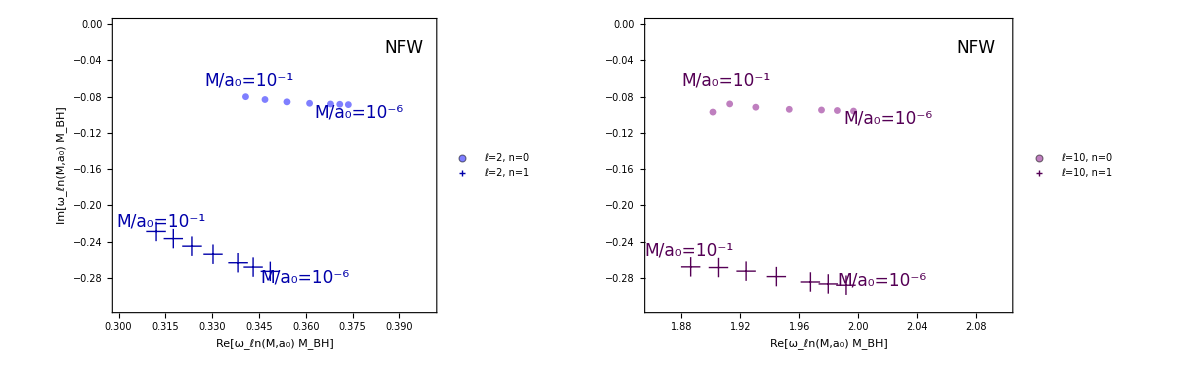

./plot/NFW_2_vs_10.pdf

```mathematica
GraphicsGrid[{{l2n,l10nA}},ImageSize->1200,Spacings->{{-20,-50},{-20,-40}}]
Export["./plot/NFW_2_vs_10.pdf",%]
```

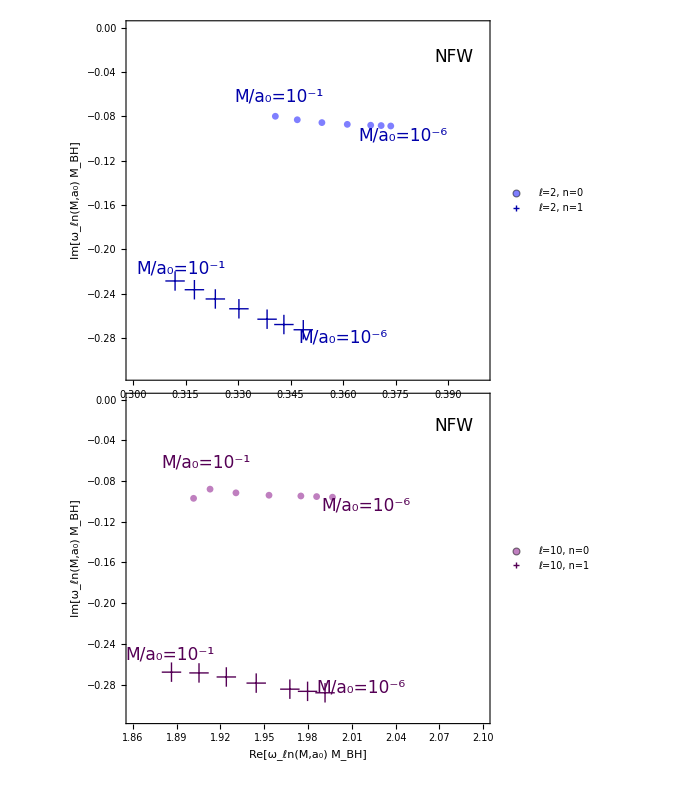

./plot/NFW_2_vs_10_col.pdf

```mathematica
GraphicsColumn[{l2nA,l10n},ImageSize->700,Spacings->-40]
Export["./plot/NFW_2_vs_10_col.pdf",%]
```